## Answers to the Mathematica worksheet

Maria Servedio 1/11/16

## 1)

```mathematica
1045*345
```

360525

## 2)

```mathematica
307^2
```

94249

## 3)

```mathematica
N[((45/6)+5)^3]
```

1953.13

## 4)

```mathematica
Simplify[(x^3+x^2 - 44  x - 84)/(x+6)]
```

-14-5 x+x^2

## 5)

```mathematica
Solve[f^2 +2 f g + 54 == g^2, f]
```

{{f→-g-√2 √(-27+g^2)},{f→-g+√2 √(-27+g^2)}}

## 6)

```mathematica
k = Table[i j,{i,2}, {j,5}]
```

{{1,2,3,4,5},{2,4,6,8,10}}

## 7)

```mathematica
TableForm[k]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10

## 8)

```mathematica
k[[1,3]]
```

3

## 9)

```mathematica
Sum[k[[2,i]], {i, 5}]
```

30

## 10)

```mathematica
D[x^8+34 x^6 +14 x^5, x]
```

70 x^4+204 x^5+8 x^7

## 11)

```mathematica
h = Table[0, {i,2},{j,5}]
```

{{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Do[h[[i,j]] = k[[i,j]] + 2, {i, 2}, {j,5}]
```

```mathematica
h
```

{{3,4,5,6,7},{4,6,8,10,12}}

## 12)

```mathematica
Plot[y^2 + 4y + 2,{y, 2,10}]
```

⁃Graphics⁃

## 13)

### 13a

```mathematica
rn1 = (1-f)rn+mn;
mn1 = f g rn;
```

### 13b

```mathematica
mn = f g rnm1;
Simplify[rn1]
```

rn-f rn+f g rnm1

### 13c

#### using the equations from part a:

```mathematica
r = 10000;
m = 1100;
f = .1;
g = 1.1;
j = 10;
```

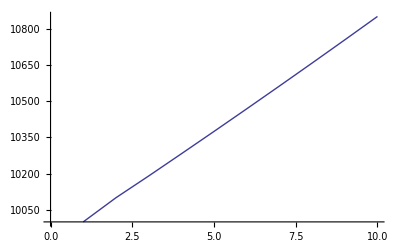

```mathematica
tabj= Table[0, {i,j}];
Do[
tabj[[i]] = r;
r1 = (1-f) r + m;
m1 = g f r;
r = r1;
m = m1,
{i,j}];
 ListPlot[tabj, Joined -> True]
```

#### using the equation from part b

```mathematica
r = 10000;
r1 = 10100;
f = .1;
g = 1.1;
```

```mathematica
tabj= Table[0, {i,j}];
Do[
tabj[[i]] = r;
r2 =(1-f) r1 + g f r;
r = r1;
r1 = r2,
{i,j}];
 ListPlot[tabj, Joined -> True]
```

-Graphics-